# Semiclassical relativistic stars

## Julio Arrechea, Carlos Barceló, Raúl Carballo-Rubio and Luis J. Garay

Instructions

This Mathematica notebook generates the plots from Figure 5

This notebook has been written in Mathematica 12.3 and should be compatible with later versions.

Any comment with a number inside a parenthesis refers to that equation in the manuscript. For instance (10) refers to equation number (10) of the manuscript.

The whole notebook can be evaluated at once through the option Evaluation -> Evaluate Notebook. Evaluation -> Dynamic updating enabled must be checked to see the figures.

### Parametrized family of geometries

Let us define the parametrized redshift and compactness functions in (11)

```mathematica
Redshift[r_,β0_,β1_,β2_]:=β1 a0[β0,β1]^(β2 (r/R)^4)+a1[β0,β1,β2] (r/R)^6 Exp[a2[β0,β1,β2] (r/R-1)];
Compactness[r_,β3_,β4_]:=β3 (Cos[(β4 r)/R]-1) Exp[-(β4 r)/R]+a3[β3,β4] (r/R)^2;
```

With the following constants (12)

```mathematica
a0[β0_,β1_]:=(1-CR+β0)/(β1 (1+β0));
a1[β0_,β1_,β2_]:=1-CR/(1+β0)-β1 a0[β0,β1]^β2;
a2[β0_,β1_,β2_]:=(2 β1 a0[β0,β1]^β2 (3-β2 Log[a0[β0,β1]])+(CR (7+6 β0))/(1+β0)^2-6)/a1[β0,β1,β2];
a3[β3_,β4_]:=β3 Exp[-β4] (1-Cos[β4])+CR;
```

### Integration parameters and numerical solutions for comparison

We will compare this family of solutions with an exact, numerical solution describing a semiclassical relativistic star. We fix the parameter β0  to a small quantity for simplicity:

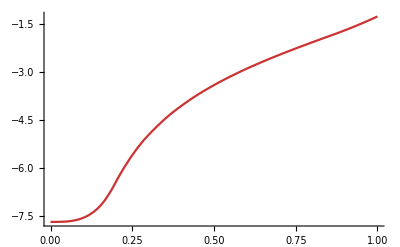
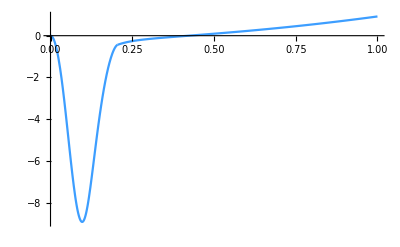
```mathematica
Params={CR->0.92,R-> 1,β0-> 10^-4};
ϕNumerical=-Graphics-;
CNumerical=-Graphics-;
```

### Plotting the solutions

Redshift function 1/2 Log ϕ:

```mathematica
Manipulate[Show[Plot[1/2Log[Redshift[r,β0,β1,β2]]/.Params,{r,0,R/.Params},PlotRange->{{0,R/.Params},{-10,0}},PlotStyle->{Dashed,RGBColor[0.75,0.5,0.1]}],ϕNumerical],{β1,5*10^-9,10^-5},{β2,0.65,0.95}]
```

Compactness function C:

```mathematica
Manipulate[Show[Plot[Compactness[r,β3,β4]/.Params,{r,0,R/.Params},PlotRange->{{0,R/.Params},{1,-10}},PlotStyle->{Dashed,RGBColor[0.24,0.8,0.62]}],CNumerical],{β3,0,45},{β4,0,50}]
```